# Initialization

```mathematica
HaToeV=27.21138602;
```

```mathematica
SizeLegend=1.5;
```

```mathematica
SetDirectory["~/Dropbox/Manuscripts/CC4/Data"];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,mathpazo,xcolor,bm,mhchem}"}];
```

# XLS

### Methods

```mathematica
Met={"CC2","CCSD","CCSDT-3","CC3","CCSDT","CC4","CCSDTQ","CCSDTQP"};
```

### Charts

```mathematica
SizeLabel=1.25;
SizeFrameLabel=2;
ChartCC3={
Frame->True,
BaseStyle->16,
BarSpacing->{0,0},
GridLines->{Automatic,All},
AspectRatio->4,
PlotTheme->"Scientific",
Joined->True,
ChartElementFunction->"Rectangle",
ImageSize->250,
BarOrigin->Left
};
```

```mathematica
BarChart[Ea⟦;;,2⟧,PlotLabel->MaTeX["\\text{Absorption energy}",Magnification->2],ChartStyle->LightBlue,
ChartCC3,PlotRange->{{-1.0,0.0},{1,Length[Ea]}},
FrameLabel->{None,MaTeX["\\text{MSE (eV)}",Magnification->SizeFrameLabel]},ChartLabels->Placed[Table[Rotate[MaTeX[StringJoin["\\text{",Ea⟦k,1⟧,"}"],Magnification->SizeLabel],0 Degree],{k,Length[Ea]}],Right]
]
Export["Figure-3a.pdf",%];
BarChart[Ef⟦;;,2⟧,PlotLabel->MaTeX["\\text{Fluorescence energy}",Magnification->2],ChartStyle->LightRed,
ChartCC3,PlotRange->{{-1.0,0.0},{1,Length[Ef]}},
FrameLabel->{None,MaTeX["\\text{MSE (eV)}",Magnification->SizeFrameLabel]},
ChartLabels->Placed[Table[Rotate[MaTeX[StringJoin["\\text{",Ef⟦k,1⟧,"}"],Magnification->SizeLabel],0 Degree],{k,Length[Ef]}],Right]
]
Export["Figure-3b.pdf",%];
BarChart[Ead⟦;;,2⟧,PlotLabel->MaTeX["\\text{Adiabatic energy}",Magnification->2],ChartStyle->LightGreen,
ChartCC3,PlotRange->{{-1.0,0.0},{1,Length[Ead]}},
FrameLabel->{None,MaTeX["\\text{MSE (eV)}",Magnification->SizeFrameLabel]},
ChartLabels->Placed[Table[Rotate[MaTeX[StringJoin["\\text{",Ead⟦k,1⟧,"}"],Magnification->SizeLabel],0 Degree],{k,Length[Ead]}],Right]
]
Export["Figure-3c.pdf",%];
```

### MSE/AVDZ

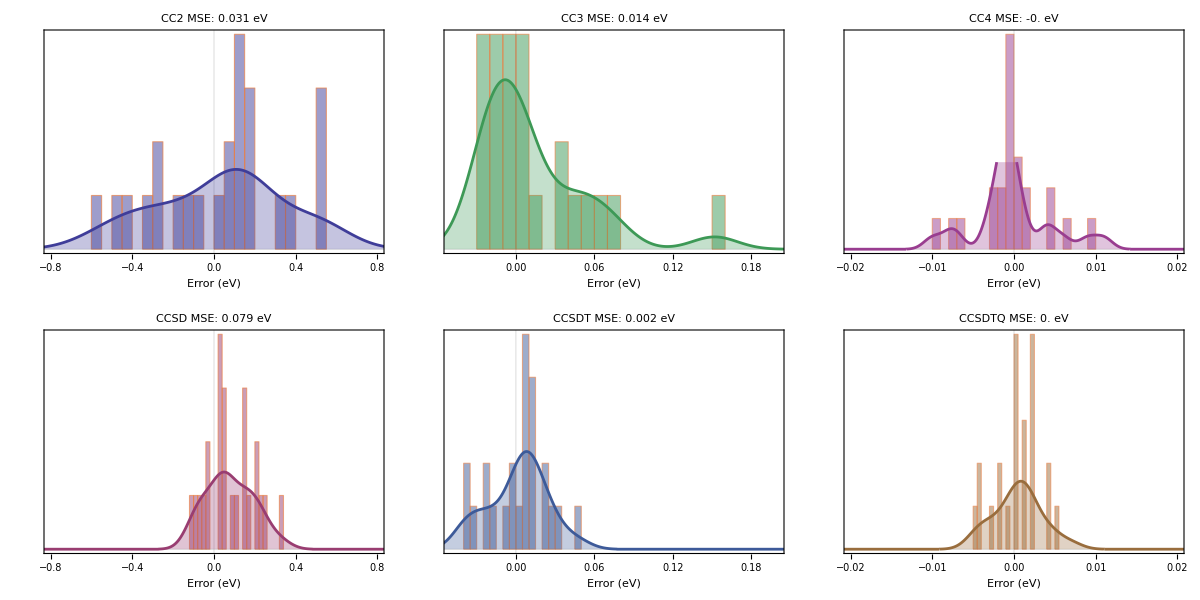

```mathematica
MSEDZ=Import["CC4-Bench.xlsx"]⟦1,4;;28,3;;10⟧;
MSEDZ=Table[MSEDZ⟦a,b⟧-MSEDZ⟦a,Length[Met]⟧,{a,Length[MSEDZ]},{b,Length[Met]-1}];
graph=Table[
Show[{
Histogram[MSEDZ⟦2;;,m⟧,20,"PDF",PlotTheme->"Scientific",BaseStyle->14,PlotRange->{{-0.1,0.1},Automatic},FrameLabel->{"Error (eV)",None},ChartStyle->{Directive[Opacity[0.5],ColorData[1,"ColorList"]⟦m⟧]},FrameTicks->{Automatic,None},PlotLabel->Style[Met⟦m⟧<>" MSE: "<>ToString[SetAccuracy[Mean[MSEDZ⟦2;;,m⟧],4]]<>" eV",12]]
,
SmoothHistogram[DeleteCases[MSEDZ⟦2;;,m⟧,""],Automatic,"PDF",PlotRange->{{-1,1},Automatic},PlotStyle->Directive[ColorData[1,"ColorList"]⟦m⟧,Thickness[0.01]],Filling->Bottom,PlotTheme->"Web"]
},ImageSize->200]
,{m,Length[Met]-1}];
Grid[
{{Show[graph⟦1⟧,PlotRange->{{-0.8,0.8},All}],
Show[graph⟦4⟧,PlotRange->{{-0.05,0.2},All}],
Show[graph⟦6⟧,PlotRange->{{-0.02,0.02},All}]
}
,
{
Show[graph⟦2⟧,PlotRange->{{-0.8,0.8},All}],
Show[graph⟦5⟧,PlotRange->{{-0.05,0.2},All}],
Show[graph⟦7⟧,PlotRange->{{-0.02,0.02},All}]
}}
]
Export["histograms_MSE_AVDZ.pdf",%];
```

### MAE/AVDZ

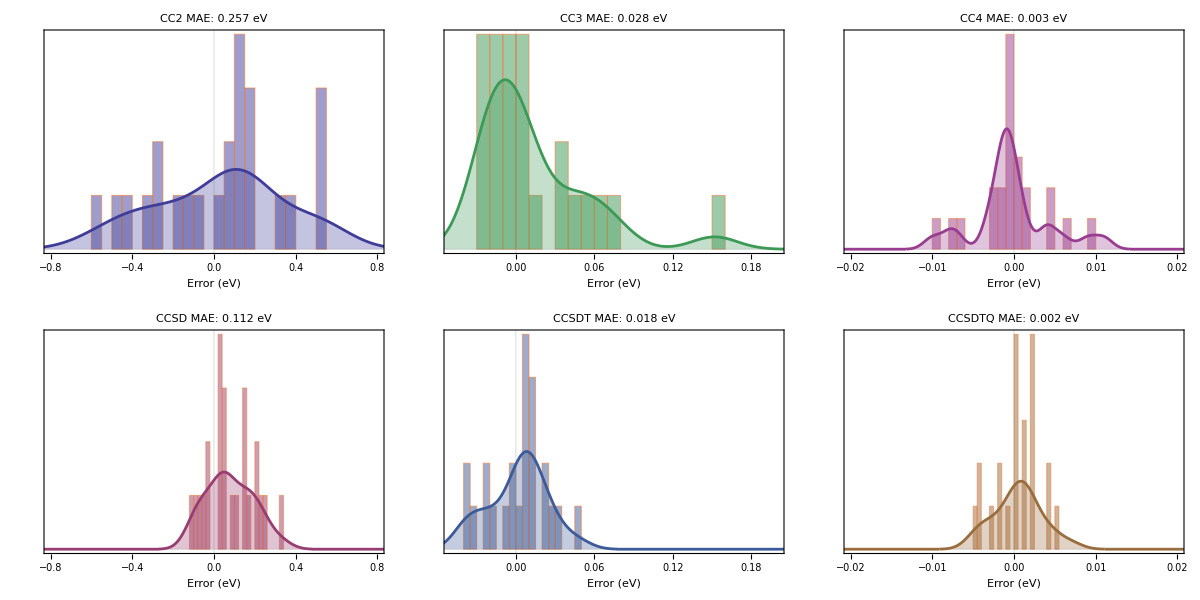

```mathematica
MAEDZ=Import["CC4-Bench.xlsx"]⟦1,4;;28,3;;10⟧;
MAEDZ=Table[MAEDZ⟦a,b⟧-MAEDZ⟦a,Length[Met]⟧,{a,Length[MAEDZ]},{b,Length[Met]-1}];
graph=Table[
Show[{
Histogram[MAEDZ⟦2;;,m⟧,20,"PDF",PlotTheme->"Scientific",BaseStyle->14,PlotRange->{{-0.25,0.25},All},FrameLabel->{"Error (eV)",None},ChartStyle->{Directive[Opacity[0.5],ColorData[1,"ColorList"]⟦m⟧]},FrameTicks->{Automatic,None},PlotLabel->Style[Met⟦m⟧<>" MAE: "<>ToString[SetAccuracy[Mean[Abs[MAEDZ⟦2;;,m⟧]],4]]<>" eV",12]]
,
SmoothHistogram[DeleteCases[MAEDZ⟦2;;,m⟧,""],Automatic,"PDF",PlotRange->{{-1,1},All},PlotStyle->Directive[ColorData[1,"ColorList"]⟦m⟧,Thickness[0.01]],Filling->Bottom,PlotTheme->"Web"]
},ImageSize->200]
,{m,Length[Met]-1}];
Grid[
{{Show[graph⟦1⟧,PlotRange->{{-0.8,0.8},All}],
Show[graph⟦4⟧,PlotRange->{{-0.05,0.2},All}],
Show[graph⟦6⟧,PlotRange->{{-0.02,0.02},All}]
}
,
{
Show[graph⟦2⟧,PlotRange->{{-0.8,0.8},All}],
Show[graph⟦5⟧,PlotRange->{{-0.05,0.2},All}],
Show[graph⟦7⟧,PlotRange->{{-0.02,0.02},All}]
}}
]
Export["histograms_MAE_AVDZ.pdf",%];
```